# Humidity in the United States

A simple exploration of the relative humidity of regions within the united states

## Motivation

I was interested in finding out what the relative humidity was in the various regions of the united states, so I took out my Wolfram Desktop and decided to explore the topic computationally so I can gain some insight.

The first thing I did was to get a list of the states of the US so I can see what I was going to be dealing with:

```mathematica
CountryData["UnitedStates","Regions"]
```

{Alabama,Alaska,Arizona,Arkansas,California,Colorado,Connecticut,Delaware,DistrictOfColumbia,Florida,Georgia,Hawaii,Idaho,Illinois,Indiana,Iowa,Kansas,Kentucky,Louisiana,Maine,Maryland,Massachusetts,Michigan,Minnesota,Mississippi,Missouri,Montana,Nebraska,Nevada,NewHampshire,NewJersey,NewMexico,NewYork,NorthCarolina,NorthDakota,Ohio,Oklahoma,Oregon,Pennsylvania,RhodeIsland,SouthCarolina,SouthDakota,Tennessee,Texas,Utah,Vermont,Virginia,Washington,WestVirginia,Wisconsin,Wyoming}

Ok so there is it, the next natural thing to do is to check out the relative humidity of the states

```mathematica
WeatherData[#, "Humidity"]&/@CountryData["UnitedStates","Regions"]
```

{0.764,$Failed,0.889,$Failed,0.885,0.879,$Failed,1.,$Failed,0.942,0.987,$Failed,$Failed,$Failed,1.,0.889,0.94,$Failed,0.914,0.883,0.939,$Failed,$Failed,$Failed,$Failed,$Failed,0.46,$Failed,0.964,$Failed,$Failed,$Failed,0.791,$Failed,$Failed,0.841,1.,1.,$Failed,$Failed,$Failed,$Failed,0.869,1.,$Failed,0.962,0.375,0.964,$Failed,$Failed,1.}

Ok, we can see that some of the states do not have available data, thus the $Failed tag, and one point of note is that this gets relative humidity which is a percentage as a float, simply multiplying by 100 and adding the percent sign would show it in percentages, but for now we need the floats because of the kinds of computations we want to do. It is also noteworthy that this values are instant values not averages over a period of time.

Next we create some variables

```mathematica
statesUS = CountryData["UnitedStates","Regions"];
```

```mathematica
humidityOfStates = WeatherData[#, "Humidity"] & /@ CountryData["UnitedStates", "Regions"];
```

Now I pair the data values, states to their relative humidity values

```mathematica
statehumiditypair = Transpose[{statesUS,humidityOfStates}]
```

{{Alabama,0.764},{Alaska,$Failed},{Arizona,0.889},{Arkansas,$Failed},{California,0.885},{Colorado,0.879},{Connecticut,$Failed},{Delaware,1.},{DistrictOfColumbia,$Failed},{Florida,0.942},{Georgia,0.987},{Hawaii,$Failed},{Idaho,$Failed},{Illinois,$Failed},{Indiana,1.},{Iowa,0.889},{Kansas,0.94},{Kentucky,$Failed},{Louisiana,0.914},{Maine,0.883},{Maryland,0.939},{Massachusetts,$Failed},{Michigan,$Failed},{Minnesota,$Failed},{Mississippi,$Failed},{Missouri,$Failed},{Montana,0.46},{Nebraska,$Failed},{Nevada,0.964},{NewHampshire,$Failed},{NewJersey,$Failed},{NewMexico,$Failed},{NewYork,0.791},{NorthCarolina,$Failed},{NorthDakota,$Failed},{Ohio,0.841},{Oklahoma,1.},{Oregon,1.},{Pennsylvania,$Failed},{RhodeIsland,$Failed},{SouthCarolina,$Failed},{SouthDakota,$Failed},{Tennessee,0.869},{Texas,1.},{Utah,$Failed},{Vermont,0.962},{Virginia,0.375},{Washington,0.964},{WestVirginia,$Failed},{Wisconsin,$Failed},{Wyoming,1.}}

We then clean up the data removing state-humidity pairs where there is no data for humidity, i.e where we have $failed

```mathematica
cleanedUpdata =Select[statehumiditypair,#[[2]] =!= $Failed&]
```

{{Alabama,0.764},{Arizona,0.889},{California,0.885},{Colorado,0.879},{Delaware,1.},{Florida,0.942},{Georgia,0.987},{Indiana,1.},{Iowa,0.889},{Kansas,0.94},{Louisiana,0.914},{Maine,0.883},{Maryland,0.939},{Montana,0.46},{Nevada,0.964},{NewYork,0.791},{Ohio,0.841},{Oklahoma,1.},{Oregon,1.},{Tennessee,0.869},{Texas,1.},{Vermont,0.962},{Virginia,0.375},{Washington,0.964},{Wyoming,1.}}

Lets visualize this data in a PieChart

```mathematica
PieChart[#[[2]]&/@cleanedUpdata,ChartLegends->(#[[1]]&/@cleanedUpdata),ChartStyle->"Pastel"]
```

-Graphics-

You can see that since the values are close to each other in magnitude one cannot make out visually which state has a higher or lower relative humidity, if you touch the sections of the chart with your mouse, a tooltip pops up to show the values. I do not personally consider this chart very informative so I will proceed with other forms of visualizing the data.

Next I obtain a list of state abbreviations

```mathematica
abbr = {"AL", "AR", "CA", "CO", "DE", "FL", "GA", "IN", "IO", "KS", 
  "LA", "ME", "MD", "MT", "NV", "NY", "OH", "OK", "OR", "TN", "TX", 
  "VT", "VA", "WA", "WY"};
```

I only got state name abbreviations for those states that have relative humidity values.

Lets do a BarChart to see if we can get any insight

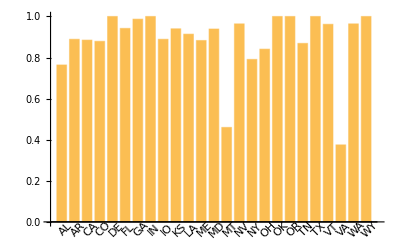

```mathematica
BarChart[#[[2]]&/@cleanedUpdata,ChartLabels-> Placed[abbr,Below,Rotate[#,Pi/4]&],BarSpacing->Automatic]
```

This looks Cleaner and we can see that the state of Virginia has the lowest humidity so far followed by Montana, but its not really clear which state has the highest relative humidity as of the present moment.

Lets visualize this on a map of the united states to see things a little clearer.

```mathematica
GeoRegionValuePlot[
 Map[(Entity[
      "AdministrativeDivision", {#[[1]], "UnitedStates"}] -> #[[
      2]]) &, cleanedUpdata]]
```

-Graphics-

I would like to know which states have the highest and lowest relative humidity so lets try this

```mathematica
SortBy[cleanedUpdata,#[[2]]&]
```

{{Virginia,0.375},{Montana,0.46},{Alabama,0.764},{NewYork,0.791},{Ohio,0.841},{Tennessee,0.869},{Colorado,0.879},{Maine,0.883},{California,0.885},{Arizona,0.889},{Iowa,0.889},{Louisiana,0.914},{Maryland,0.939},{Kansas,0.94},{Florida,0.942},{Vermont,0.962},{Nevada,0.964},{Washington,0.964},{Georgia,0.987},{Delaware,1.},{Indiana,1.},{Oklahoma,1.},{Oregon,1.},{Texas,1.},{Wyoming,1.}}

By eye balling the list we can see that the relative humidity in several states is 100 percent Lets try to extract them out of the main list

```mathematica
Select[SortBy[cleanedUpdata,#[[2]]&],(#[[2]]==1&)]
```

{{Delaware,1.},{Indiana,1.},{Oklahoma,1.},{Oregon,1.},{Texas,1.},{Wyoming,1.}}

And the state with the lowest relative humidity is:

```mathematica
SortBy[cleanedUpdata,#[[2]]&][[1]]
```

{Virginia,0.375}

Lets see a line plot of the data:

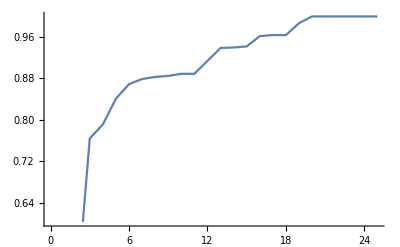

```mathematica
ListLinePlot[#[[2]]&/@SortBy[cleanedUpdata,#[[2]]&]]
```

Looks fairly like some stair case!

#### Further Exploration

This exploration is more focused on the united states and deals with the current relative humidity. The data will definitely change everytime the notebook is executed. Further work will be to get the relative humidity of a particular region for a period of time and run some analysis.

I would also like to see how this long range values compare from state to state.

The next obvious step would be to take the exploration global by doing it for the whole planet. Interesting information to find would be the most humid region/ regions on earth and how this relates to precipitation.

#### Authorship information

Jackreece Ejini

23rd June 2017

jackreeceejini@gmail.com